# Coalescent Times: Allele Surfing 3_13

## Constant population size

## Coalescent time plot

```mathematica
nPop=1;
gmax=1500;
nIndList=Flatten[Transpose[Import["/Users/ailenemacpherson/Documents/workspace/AlleleSurfing3_13/data2.csv"][[;;,1;;nPop]]]];
nInd0=nIndList[[1]];
nIndF=nIndList[[gmax+1]];
(*Important coalescent data.Each column represents the history of the different lineage.This generation in this history is captured by three rows:row 3*g+1:lineage population in generation g.row 3*g+2:lineage individual in generation g,row 3*g+2:lineage chromosome in generation g.*)
cData=Import["/Users/ailenemacpherson/Documents/workspace/AlleleSurfing3_13/coal0.csv"][[1;;3(gmax+2),1;;2*nIndF]];
sampleSize=3;
testSample=RandomSample[Range[2*nIndF],sampleSize]
```

{743,67,329}

plotData combines the info from the three identity pieces of information (population, individual, chromosome).  Each row is an lineage, each column is a generation, sub column 1= locus identity, sub column 2 is the generation.

```mathematica
plotData=Transpose[Table[{cData[[3*g+3,i]]+2*cData[[3*g+2,i]]+(2*nInd0)cData[[3*g+1,i]],gmax+1-g},{g,0,gmax+1},{i,1,2*nIndF}]];
```

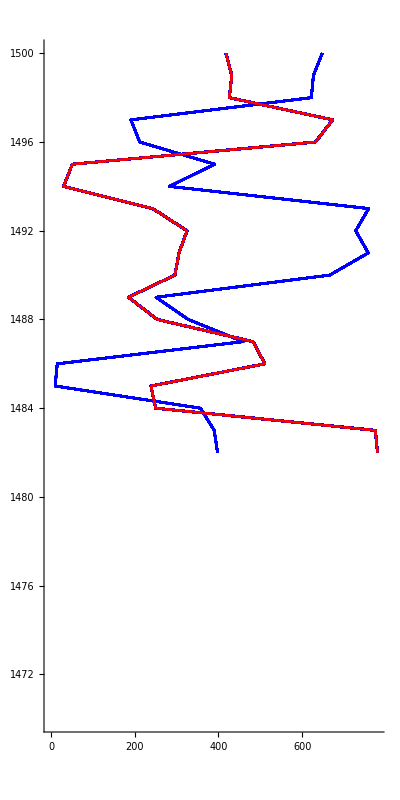

```mathematica
AllLineages=ListLinePlot[plotData[[;;,1;;20]],PlotStyle->Blue,AxesOrigin->{-1,0},AspectRatio->2,PlotRange->{1470,1500}];
SelectedLineages=ListLinePlot[plotData[[testSample]][[;;,1;;20]],PlotStyle->{Red},AxesOrigin->{-1,0},AspectRatio->2,PlotRange->{1470,1500}];
Show[AllLineages,SelectedLineages]
```

## Distribution of coalescent times in one simulation

### Calculating coalescent times for a sub-sample of the data:

For the sub-sample each row is a generation each column is an individual and the sub columns give locus identity and generation

```mathematica
Tlist[sample_]:=Block[{s,g,Tlist,T,nDistinct,sampleData},Tlist={};
sampleData=Transpose[plotData[[sample]]][[;;,;;,1]];
nDistinct=Table[CountDistinct[sampleData[[r]]],{r,1,gmax+2}];
g=gmax+2;
For[s=nDistinct[[gmax+2]],s>=nDistinct[[1]],s--,T=0;
While[nDistinct[[g]]==s,
g--;T++;
];
AppendTo[Tlist,{s,T}];
];
Tlist
];
```

```mathematica
Tlist[testSample]
```

{{3,88},{2,160},{1,1254}}

#### Distribution of coalescent times in one simulation:

Given a particular demographic history as described by nInd we can calculate the probability distribution of coalescent times by resampling.

```mathematica
Clear[tlist]
```

```mathematica
TLIST[nRep_]:=Module[{rep,tlist},tlist={};
For[rep=1,rep≤nRep,rep++,
sample=RandomSample[Range[nIndF*2],sampleSize];
AppendTo[tlist,Tlist[sample]];.10
]; tlist
];
```

```mathematica
TLIST[2]
```

{{{3,344},{2,98},{1,1060}},{{3,240},{2,44},{1,1218}}}

```mathematica
distData=TLIST[100][[;;,1;;2,2]];
```

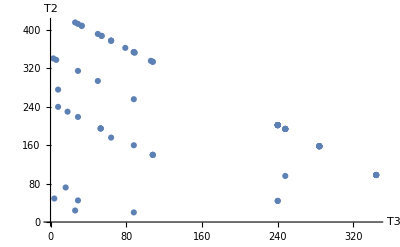

```mathematica
ListPlot[Select[distData,Total[#]<600&],AxesLabel->{"T3","T2"}]
```

```mathematica
Histogram3D[Select[distData,Total[#]<600&],PlotTheme->"Scientific",AxesLabel->{"T3","T2","Prob"}]
```

-Graphics3D-

## Distribution from multiple simulations

```mathematica
Tlist2[sampleData_]:=Block[{s,g,Tlist,T},Tlist={};
nDistinct=Table[CountDistinct[sampleData[[r]]],{r,1,gmax+2}];
g=gmax+2;
For[s=nDistinct[[gmax+2]],s>=nDistinct[[1]],s--,T=0;
While[nDistinct[[g]]==s,
g--;T++;
];
AppendTo[Tlist,{s,T}];
];
Tlist
];
```

```mathematica
nPop=1;
gmax=1500;
nRep=40;
sampleSize=3;
Module[{r,tList},TLIST={};
For[r=0,r<nRep,r++,
nIndList=Flatten[Transpose[Import[StringJoin["/Users/ailenemacpherson/Documents/workspace/AlleleSurfing3_13/data",ToString[r],".csv"]][[;;,1;;nPop]]]];
nInd0=nIndList[[1]];
nIndF=nIndList[[gmax+1]];
cData=Import[StringJoin["/Users/ailenemacpherson/Documents/workspace/AlleleSurfing3_13/coal",ToString[r],".csv"]][[1;;3(gmax+2),1;;2*nIndF]];
sample=RandomSample[Range[2nIndF],sampleSize];
sampleData=Table[cData[[3*g+3,i]]+2*cData[[3*g+2,i]]+(2*nInd0)cData[[3*g+1,i]],{g,0,gmax+1},{i,1,2*nIndF}][[;;,sample]];
tList=Tlist2[sampleData];If[nDistinct[[1]]==1,AppendTo[TLIST,tList]];
]
]
```

$Aborted

```mathematica
TLIST;
```

```mathematica
distData=Select[TLIST[[;;,{2,1},2]],#[[1]]+#[[2]]<600&];
```

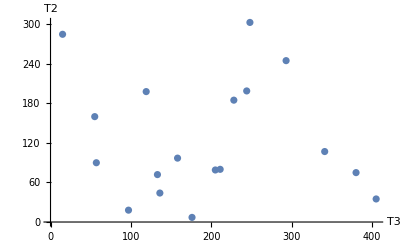

```mathematica
ListPlot[distData,AxesLabel->{"T3","T2"}]
```

```mathematica
Histogram3D[1/800 distData,AxesLabel->{"T2","T3","Prob"}]
```

-Graphics3D-

### Griffiths and Tavere predicted distribution

```mathematica
m[t_]:=2*400;
v[τ_]:=m[Floor[m[0]τ]]/m[0]
(*Note the change of Λ to a sum rather than an integral*)
Λ[x_]:=Integrate[1/v[τ],{τ,0,x}];
s[j_,i_,τVec_]:=If[j<i,Sum[τVec[[k]],{k,j,i}],If[j==i,τVec[[i]],0]];
g[i_,τVec_]:=N[Product[Binomial[j,2]/v[s[j,i,τVec]] Exp[-Binomial[j,2](Λ[s[j,i,τVec]]-Λ[s[j+1,i,τVec]])],{j,2,i}]]
```

For a population of constant size g should be identical to the standard coalescent:

```mathematica
f[i_,τVec_]:=N[Product[Binomial[j,2]Exp[-Binomial[j,2]τVec[[j]]],{j,2,i}]]
```

```mathematica
predDist=Table[{i,j,g[3,{0,i,j}]},{i,0,gmax/m[0],1/m[0]},{j,0,gmax/m[0]-i,1/m[0]}];
(*ListPlot3D[Flatten[predDist,1],Mesh->None,AxesLabel->{"T2","T3","Prob"},InterpolationOrder->1,PlotRange->All]*)
```

Note that this conditional (t2+t3<gmax) probability distribution is NOT normalized to a volume of 1.

```mathematica
totalProb=(1/m[0])^2 Total[Flatten[predDist,1][[;;,3]]]
```

0.774124

In order to calculate the probability a coalescent time combination falls in any given real generation combination (x,y)

```mathematica
prob[x_,y_]:=(1/m[0])^2*predDist[[x+1,y+1,3]]/totalProb
```

## Log likelihood calculation

Constant population size likelihood

```mathematica
Hconst[popSize_,gmax_]:=Block[{i,m,v,Λ,s,g,L},L=0;
m[t_]:=2*popSize;
v[τ_]:=m[Floor[m[0]τ]]/m[0];
Λ[x_]:=Integrate[1/v[τ],{τ,0,x}];
s[j_,i_,τVec_]:=If[j<i,Sum[τVec[[k]],{k,j,i}],If[j==i,τVec[[i]],0]];
g[i_,τVec_]:=N[Product[Binomial[j,2]/v[s[j,i,τVec]] Exp[-Binomial[j,2](Λ[s[j,i,τVec]]-Λ[s[j+1,i,τVec]])],{j,2,i}]];
predDist=Table[{i,j,g[3,{0,i,j}]},{i,0,gmax/m[0],1/m[0]},{j,0,gmax/m[0]-i,1/m[0]}];
totalProb=(1/m[0])^2 Total[Flatten[predDist,1][[;;,3]]];
prob[x_,y_]:=(1/m[0])^2*predDist[[x+1,y+1,3]]/totalProb;
For[i=1,i≤Length[distData],i++,
L+=Log[prob[distData[[i,1]],distData[[i,2]]]];
];
L
]
```

```mathematica
Hconst[400,1500]
```

-229.185

```mathematica
Llist=Table[{x,Hconst[x,1500]},{x,50,550,50}]
```

{{50,-249.75},{100,-222.819},{150,-219.959},{200,-221.209},{250,-223.307},{300,-225.451},{350,-227.426},{400,-229.185},{450,-230.738},{500,-232.105},{550,-233.314}}

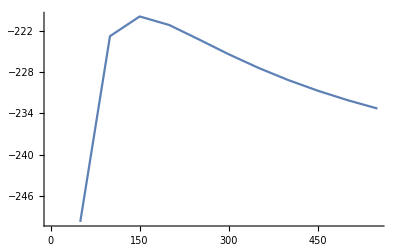

```mathematica
ListLinePlot[Llist]
```

### Save TLIST

```mathematica
TLIST={{{3,45},{2,264},{1,293}},{{3,78},{2,147},{1,377}},{{3,98},{2,503},{1,1}},{{3,134},{2,467},{1,1}},{{3,20},{2,339},{1,243}},{{3,53},{2,100},{1,449}},{{3,151},{2,24},{1,427}},{{3,300},{2,301},{1,1}},{{3,283},{2,4},{1,315}},{{3,509},{2,92},{1,1}},{{3,419},{2,43},{1,140}},{{3,56},{2,545},{1,1}},{{3,75},{2,2},{1,525}},{{3,454},{2,147},{1,1}},{{3,392},{2,14},{1,196}},{{3,544},{2,57},{1,1}},{{3,34},{2,567},{1,1}},{{3,211},{2,390},{1,1}},{{3,259},{2,62},{1,281}},{{3,229},{2,372},{1,1}},{{3,56},{2,52},{1,494}},{{3,106},{2,348},{1,148}},{{3,3},{2,441},{1,158}},{{3,220},{2,381},{1,1}},{{3,78},{2,419},{1,105}},{{3,43},{2,51},{1,508}},{{3,85},{2,57},{1,460}},{{3,89},{2,237},{1,276}},{{3,55},{2,316},{1,231}},{{3,210},{2,141},{1,251}},{{3,183},{2,418},{1,1}},{{3,25},{2,267},{1,310}},{{3,176},{2,265},{1,161}},{{3,28},{2,573},{1,1}},{{3,119},{2,482},{1,1}},{{3,80},{2,142},{1,380}},{{3,143},{2,446},{1,13}},{{3,19},{2,161},{1,422}},{{3,43},{2,511},{1,48}},{{3,76},{2,217},{1,309}},{{3,413},{2,188},{1,1}},{{3,114},{2,42},{1,446}},{{3,2},{2,599},{1,1}},{{3,109},{2,139},{1,354}},{{3,102},{2,137},{1,363}},{{3,46},{2,24},{1,532}},{{3,569},{2,32},{1,1}},{{3,302},{2,43},{1,257}},{{3,140},{2,461},{1,1}},{{3,106},{2,3},{1,493}},{{3,94},{2,9},{1,499}},{{3,147},{2,454},{1,1}},{{3,92},{2,75},{1,435}},{{3,209},{2,392},{1,1}},{{3,136},{2,465},{1,1}},{{3,65},{2,536},{1,1}},{{3,204},{2,85},{1,313}},{{3,90},{2,49},{1,463}},{{3,305},{2,296},{1,1}},{{3,106},{2,495},{1,1}},{{3,8},{2,121},{1,473}},{{3,32},{2,130},{1,440}},{{3,312},{2,195},{1,95}},{{3,48},{2,445},{1,109}},{{3,11},{2,496},{1,95}},{{3,107},{2,431},{1,64}},{{3,36},{2,116},{1,450}},{{3,214},{2,387},{1,1}},{{3,152},{2,449},{1,1}},{{3,87},{2,349},{1,166}},{{3,90},{2,63},{1,449}},{{3,104},{2,497},{1,1}},{{3,238},{2,210},{1,154}},{{3,424},{2,118},{1,60}},{{3,136},{2,130},{1,336}},{{3,245},{2,356},{1,1}},{{3,48},{2,553},{1,1}},{{3,104},{2,386},{1,112}},{{3,111},{2,490},{1,1}},{{3,126},{2,81},{1,395}},{{3,51},{2,177},{1,374}},{{3,350},{2,87},{1,165}},{{3,100},{2,356},{1,146}},{{3,1},{2,600},{1,1}},{{3,86},{2,151},{1,365}},{{3,15},{2,456},{1,131}},{{3,123},{2,95},{1,384}},{{3,113},{2,252},{1,237}},{{3,83},{2,14},{1,505}},{{3,13},{2,567},{1,22}},{{3,172},{2,103},{1,327}},{{3,124},{2,165},{1,313}},{{3,222},{2,333},{1,47}},{{3,71},{2,176},{1,355}},{{3,256},{2,150},{1,196}},{{3,28},{2,490},{1,84}},{{3,220},{2,381},{1,1}},{{3,464},{2,137},{1,1}},{{3,134},{2,19},{1,449}},{{3,90},{2,72},{1,440}},{{3,97},{2,301},{1,204}},{{3,11},{2,67},{1,524}},{{3,24},{2,520},{1,58}},{{3,12},{2,162},{1,428}},{{3,36},{2,552},{1,14}},{{3,61},{2,99},{1,442}},{{3,199},{2,402},{1,1}},{{3,100},{2,501},{1,1}},{{3,284},{2,142},{1,176}},{{3,84},{2,321},{1,197}},{{3,52},{2,499},{1,51}},{{3,35},{2,566},{1,1}},{{3,57},{2,103},{1,442}},{{3,10},{2,591},{1,1}},{{3,328},{2,273},{1,1}},{{3,74},{2,527},{1,1}},{{3,30},{2,63},{1,509}},{{3,169},{2,407},{1,26}},{{3,81},{2,81},{1,440}},{{3,37},{2,47},{1,518}},{{3,79},{2,100},{1,423}},{{3,397},{2,17},{1,188}},{{3,90},{2,288},{1,224}},{{3,98},{2,102},{1,402}},{{3,9},{2,222},{1,371}},{{3,25},{2,316},{1,261}},{{3,63},{2,538},{1,1}},{{3,24},{2,512},{1,66}},{{3,133},{2,16},{1,453}},{{3,81},{2,141},{1,380}},{{3,23},{2,578},{1,1}},{{3,26},{2,424},{1,152}},{{3,251},{2,77},{1,274}},{{3,65},{2,37},{1,500}},{{3,28},{2,255},{1,319}},{{3,18},{2,40},{1,544}},{{3,157},{2,444},{1,1}},{{3,534},{2,47},{1,21}},{{3,190},{2,155},{1,257}},{{3,50},{2,467},{1,85}},{{3,293},{2,75},{1,234}},{{3,68},{2,533},{1,1}},{{3,1},{2,90},{1,511}},{{3,26},{2,45},{1,531}},{{3,19},{2,282},{1,301}},{{3,227},{2,24},{1,351}},{{3,63},{2,197},{1,342}},{{3,232},{2,165},{1,205}},{{3,41},{2,269},{1,292}},{{3,63},{2,393},{1,146}},{{3,78},{2,253},{1,271}},{{3,398},{2,203},{1,1}},{{3,172},{2,110},{1,320}},{{3,123},{2,17},{1,462}},{{3,159},{2,360},{1,83}},{{3,246},{2,10},{1,346}},{{3,55},{2,203},{1,344}},{{3,74},{2,250},{1,278}},{{3,265},{2,336},{1,1}},{{3,100},{2,95},{1,407}},{{3,110},{2,491},{1,1}},{{3,18},{2,22},{1,562}},{{3,94},{2,94},{1,414}},{{3,87},{2,46},{1,469}},{{3,22},{2,38},{1,542}},{{3,280},{2,212},{1,110}},{{3,60},{2,64},{1,478}},{{3,184},{2,273},{1,145}},{{3,13},{2,150},{1,439}},{{3,107},{2,163},{1,332}},{{3,65},{2,156},{1,381}},{{3,43},{2,362},{1,197}},{{3,103},{2,486},{1,13}},{{3,3},{2,268},{1,331}},{{3,73},{2,528},{1,1}},{{3,39},{2,6},{1,557}},{{3,121},{2,314},{1,167}},{{3,190},{2,253},{1,159}},{{3,266},{2,229},{1,107}},{{3,21},{2,474},{1,107}},{{3,261},{2,340},{1,1}},{{3,128},{2,473},{1,1}},{{3,46},{2,363},{1,193}},{{3,198},{2,20},{1,384}},{{3,9},{2,53},{1,540}},{{3,11},{2,160},{1,431}},{{3,36},{2,57},{1,509}},{{3,83},{2,85},{1,434}},{{3,115},{2,150},{1,337}},{{3,23},{2,107},{1,472}},{{3,83},{2,208},{1,311}},{{3,40},{2,561},{1,1}},{{3,38},{2,369},{1,195}},{{3,233},{2,368},{1,1}},{{3,547},{2,54},{1,1}},{{3,35},{2,389},{1,178}},{{3,188},{2,180},{1,234}},{{3,465},{2,136},{1,1}},{{3,380},{2,221},{1,1}},{{3,220},{2,60},{1,322}},{{3,181},{2,101},{1,320}},{{3,57},{2,430},{1,115}},{{3,66},{2,535},{1,1}},{{3,58},{2,210},{1,334}},{{3,60},{2,541},{1,1}},{{3,273},{2,316},{1,13}},{{3,19},{2,261},{1,322}},{{3,201},{2,167},{1,234}},{{3,228},{2,1},{1,373}},{{3,79},{2,259},{1,264}},{{3,60},{2,253},{1,289}},{{3,292},{2,24},{1,286}},{{3,40},{2,327},{1,235}},{{3,448},{2,78},{1,76}},{{3,601},{2,0},{1,1}},{{3,28},{2,573},{1,1}},{{3,83},{2,421},{1,98}},{{3,108},{2,252},{1,242}},{{3,51},{2,550},{1,1}},{{3,256},{2,215},{1,131}},{{3,41},{2,553},{1,8}},{{3,99},{2,45},{1,458}},{{3,144},{2,349},{1,109}},{{3,106},{2,12},{1,484}},{{3,44},{2,490},{1,68}},{{3,5},{2,14},{1,583}},{{3,158},{2,253},{1,191}},{{3,78},{2,523},{1,1}},{{3,6},{2,115},{1,481}},{{3,4},{2,597},{1,1}},{{3,137},{2,464},{1,1}},{{3,63},{2,538},{1,1}},{{3,171},{2,360},{1,71}},{{3,111},{2,146},{1,345}},{{3,21},{2,580},{1,1}},{{3,26},{2,94},{1,482}},{{3,40},{2,561},{1,1}},{{3,123},{2,77},{1,402}},{{3,70},{2,531},{1,1}},{{3,44},{2,155},{1,403}},{{3,41},{2,50},{1,511}},{{3,34},{2,567},{1,1}},{{3,234},{2,367},{1,1}},{{3,33},{2,568},{1,1}},{{3,9},{2,71},{1,522}},{{3,11},{2,179},{1,412}},{{3,97},{2,210},{1,295}},{{3,15},{2,147},{1,440}},{{3,11},{2,56},{1,535}},{{3,218},{2,383},{1,1}},{{3,12},{2,0},{1,590}},{{3,78},{2,235},{1,289}},{{3,57},{2,78},{1,467}},{{3,86},{2,515},{1,1}},{{3,11},{2,2},{1,589}},{{3,77},{2,427},{1,98}},{{3,27},{2,185},{1,390}},{{3,155},{2,403},{1,44}},{{3,52},{2,549},{1,1}},{{3,85},{2,93},{1,424}},{{3,3},{2,598},{1,1}},{{3,74},{2,527},{1,1}},{{3,21},{2,580},{1,1}},{{3,23},{2,93},{1,486}},{{3,58},{2,543},{1,1}},{{3,71},{2,208},{1,323}},{{3,36},{2,49},{1,517}},{{3,240},{2,361},{1,1}},{{3,214},{2,126},{1,262}},{{3,75},{2,24},{1,503}},{{3,4},{2,45},{1,553}},{{3,197},{2,310},{1,95}},{{3,76},{2,88},{1,438}},{{3,23},{2,578},{1,1}},{{3,549},{2,52},{1,1}},{{3,116},{2,485},{1,1}},{{3,6},{2,595},{1,1}},{{3,220},{2,381},{1,1}},{{3,55},{2,546},{1,1}},{{3,52},{2,50},{1,500}},{{3,395},{2,19},{1,188}},{{3,45},{2,556},{1,1}},{{3,182},{2,419},{1,1}},{{3,278},{2,296},{1,28}},{{3,307},{2,119},{1,176}},{{3,107},{2,494},{1,1}},{{3,222},{2,379},{1,1}},{{3,32},{2,569},{1,1}},{{3,110},{2,211},{1,281}},{{3,87},{2,201},{1,314}},{{3,46},{2,69},{1,487}},{{3,64},{2,537},{1,1}},{{3,307},{2,90},{1,205}},{{3,134},{2,42},{1,426}},{{3,144},{2,24},{1,434}},{{3,33},{2,172},{1,397}},{{3,187},{2,2},{1,413}},{{3,60},{2,184},{1,358}},{{3,92},{2,509},{1,1}},{{3,381},{2,220},{1,1}},{{3,199},{2,65},{1,338}},{{3,50},{2,551},{1,1}},{{3,26},{2,575},{1,1}},{{3,311},{2,290},{1,1}},{{3,44},{2,454},{1,104}},{{3,222},{2,212},{1,168}},{{3,9},{2,510},{1,83}},{{3,117},{2,484},{1,1}},{{3,32},{2,57},{1,513}},{{3,18},{2,74},{1,510}},{{3,178},{2,229},{1,195}},{{3,62},{2,396},{1,144}},{{3,61},{2,540},{1,1}},{{3,90},{2,511},{1,1}},{{3,31},{2,15},{1,556}},{{3,122},{2,342},{1,138}},{{3,17},{2,141},{1,444}},{{3,348},{2,61},{1,193}},{{3,47},{2,554},{1,1}},{{3,19},{2,23},{1,560}},{{3,254},{2,347},{1,1}},{{3,147},{2,300},{1,155}},{{3,79},{2,349},{1,174}},{{3,118},{2,55},{1,429}},{{3,28},{2,48},{1,526}},{{3,91},{2,469},{1,42}},{{3,9},{2,355},{1,238}},{{3,143},{2,458},{1,1}},{{3,154},{2,406},{1,42}},{{3,52},{2,549},{1,1}},{{3,32},{2,430},{1,140}},{{3,35},{2,424},{1,143}},{{3,33},{2,288},{1,281}},{{3,35},{2,566},{1,1}},{{3,62},{2,539},{1,1}},{{3,63},{2,153},{1,386}},{{3,16},{2,68},{1,518}},{{3,28},{2,573},{1,1}},{{3,6},{2,177},{1,419}},{{3,11},{2,176},{1,415}},{{3,94},{2,98},{1,410}},{{3,4},{2,109},{1,489}},{{3,358},{2,243},{1,1}},{{3,36},{2,27},{1,539}},{{3,44},{2,386},{1,172}},{{3,19},{2,582},{1,1}},{{3,26},{2,26},{1,550}},{{3,115},{2,486},{1,1}},{{3,71},{2,530},{1,1}},{{3,76},{2,342},{1,184}},{{3,241},{2,198},{1,163}},{{3,90},{2,260},{1,252}},{{3,301},{2,109},{1,192}},{{3,313},{2,288},{1,1}},{{3,202},{2,125},{1,275}},{{3,24},{2,350},{1,228}},{{3,138},{2,197},{1,267}},{{3,45},{2,70},{1,487}},{{3,80},{2,94},{1,428}},{{3,112},{2,171},{1,319}},{{3,164},{2,168},{1,270}},{{3,421},{2,4},{1,177}},{{3,93},{2,62},{1,447}},{{3,262},{2,94},{1,246}},{{3,26},{2,186},{1,390}},{{3,238},{2,133},{1,231}},{{3,155},{2,65},{1,382}},{{3,93},{2,393},{1,116}},{{3,94},{2,237},{1,271}},{{3,97},{2,503},{1,2}},{{3,81},{2,425},{1,96}},{{3,39},{2,18},{1,545}},{{3,509},{2,92},{1,1}},{{3,3},{2,122},{1,477}},{{3,75},{2,503},{1,24}},{{3,115},{2,486},{1,1}},{{3,256},{2,345},{1,1}},{{3,83},{2,48},{1,471}},{{3,28},{2,319},{1,255}},{{3,67},{2,534},{1,1}},{{3,6},{2,114},{1,482}},{{3,1},{2,600},{1,1}},{{3,15},{2,540},{1,47}},{{3,5},{2,91},{1,506}},{{3,205},{2,361},{1,36}},{{3,77},{2,480},{1,45}},{{3,141},{2,194},{1,267}},{{3,270},{2,154},{1,178}},{{3,19},{2,523},{1,60}},{{3,409},{2,29},{1,164}},{{3,1},{2,90},{1,511}},{{3,339},{2,90},{1,173}},{{3,336},{2,126},{1,140}},{{3,191},{2,107},{1,304}},{{3,173},{2,428},{1,1}},{{3,9},{2,52},{1,541}},{{3,140},{2,73},{1,389}},{{3,12},{2,588},{1,2}},{{3,11},{2,231},{1,360}},{{3,61},{2,326},{1,215}},{{3,270},{2,196},{1,136}},{{3,601},{2,0},{1,1}},{{3,14},{2,15},{1,573}},{{3,117},{2,484},{1,1}},{{3,47},{2,554},{1,1}},{{3,55},{2,546},{1,1}},{{3,140},{2,400},{1,62}},{{3,168},{2,21},{1,413}},{{3,118},{2,466},{1,18}},{{3,56},{2,545},{1,1}},{{3,443},{2,8},{1,151}},{{3,38},{2,14},{1,550}},{{3,37},{2,241},{1,324}},{{3,159},{2,442},{1,1}},{{3,99},{2,304},{1,199}},{{3,3},{2,27},{1,572}},{{3,45},{2,556},{1,1}},{{3,166},{2,321},{1,115}},{{3,40},{2,262},{1,300}},{{3,147},{2,281},{1,174}},{{3,207},{2,394},{1,1}},{{3,423},{2,178},{1,1}},{{3,18},{2,51},{1,533}},{{3,367},{2,234},{1,1}},{{3,202},{2,399},{1,1}},{{3,39},{2,50},{1,513}},{{3,79},{2,138},{1,385}},{{3,47},{2,286},{1,269}},{{3,61},{2,185},{1,356}},{{3,247},{2,251},{1,104}},{{3,67},{2,156},{1,379}},{{3,59},{2,447},{1,96}},{{3,502},{2,99},{1,1}},{{3,143},{2,169},{1,290}},{{3,195},{2,406},{1,1}},{{3,47},{2,34},{1,521}},{{3,161},{2,159},{1,282}},{{3,245},{2,344},{1,13}},{{3,39},{2,9},{1,554}},{{3,50},{2,551},{1,1}},{{3,206},{2,107},{1,289}},{{3,180},{2,421},{1,1}},{{3,167},{2,93},{1,342}},{{3,7},{2,153},{1,442}},{{3,226},{2,74},{1,302}},{{3,203},{2,184},{1,215}},{{3,141},{2,279},{1,182}},{{3,11},{2,590},{1,1}},{{3,17},{2,9},{1,576}},{{3,217},{2,230},{1,155}},{{3,35},{2,287},{1,280}},{{3,154},{2,447},{1,1}},{{3,81},{2,172},{1,349}},{{3,117},{2,484},{1,1}},{{3,36},{2,565},{1,1}},{{3,223},{2,378},{1,1}},{{3,476},{2,66},{1,60}},{{3,65},{2,306},{1,231}},{{3,77},{2,168},{1,357}},{{3,434},{2,167},{1,1}},{{3,54},{2,273},{1,275}},{{3,39},{2,6},{1,557}},{{3,133},{2,102},{1,367}},{{3,222},{2,294},{1,86}},{{3,77},{2,125},{1,400}},{{3,78},{2,53},{1,471}},{{3,601},{2,0},{1,1}},{{3,33},{2,535},{1,34}},{{3,29},{2,489},{1,84}},{{3,125},{2,181},{1,296}},{{3,71},{2,258},{1,273}},{{3,177},{2,249},{1,176}},{{3,10},{2,131},{1,461}},{{3,85},{2,234},{1,283}},{{3,218},{2,114},{1,270}},{{3,130},{2,109},{1,363}},{{3,531},{2,70},{1,1}},{{3,9},{2,266},{1,327}},{{3,145},{2,113},{1,344}},{{3,163},{2,108},{1,331}},{{3,133},{2,1},{1,468}},{{3,205},{2,265},{1,132}},{{3,57},{2,544},{1,1}},{{3,252},{2,349},{1,1}},{{3,96},{2,120},{1,386}},{{3,120},{2,296},{1,186}},{{3,51},{2,550},{1,1}},{{3,7},{2,510},{1,85}},{{3,70},{2,176},{1,356}},{{3,83},{2,49},{1,470}},{{3,238},{2,326},{1,38}},{{3,161},{2,440},{1,1}},{{3,44},{2,105},{1,453}},{{3,35},{2,55},{1,512}},{{3,3},{2,454},{1,145}},{{3,205},{2,396},{1,1}},{{3,244},{2,24},{1,334}},{{3,157},{2,444},{1,1}},{{3,56},{2,187},{1,359}}};
```